## Definations

```mathematica
Γx={{0,(-√3)/4,0,3/4},{(-√3)/4,0,1/4,0},{0,1/4,0,(-√3)/4},{3/4,0,(-√3)/4,0}};
Γy={{0,(ⅈ √3)/4,0,(ⅈ 3)/4},{(-ⅈ √3)/4,0,-ⅈ/4,0},{0,ⅈ/4,0,(ⅈ √3)/4},{(-ⅈ 3)/4,0,(-ⅈ √3)/4,0}};
Γz={{0,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,0}};
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
```

```mathematica
Sx.Sx.Sx//MatrixForm
Sy.Sy.Sy//MatrixForm
Sz.Sz.Sz//MatrixForm
Sx//MatrixForm
Sy//MatrixForm
Sz//MatrixForm
```

(0 | (7 √3)/8 | 0 | 3/4
(7 √3)/8 | 0 | 5/2 | 0
0 | 5/2 | 0 | (7 √3)/8
3/4 | 0 | (7 √3)/8 | 0)

(0 | -(7 ⅈ √3)/8 | 0 | (3 ⅈ)/4
(7 ⅈ √3)/8 | 0 | -(5 ⅈ)/2 | 0
0 | (5 ⅈ)/2 | 0 | -(7 ⅈ √3)/8
-(3 ⅈ)/4 | 0 | (7 ⅈ √3)/8 | 0)

(27/8 | 0 | 0 | 0
0 | 1/8 | 0 | 0
0 | 0 | -1/8 | 0
0 | 0 | 0 | -27/8)

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

```mathematica
H[kx_,ky_,kz_,δ_]:=v( kx Sx+ky Sy +kz Sz)+v δ (kx Sx.Sx.Sx+ky Sy.Sy.Sy+kz Sz.Sz.Sz);
H[kx,ky,kz,δ]//MatrixForm
```

((3 kz v)/2+(27 kz v δ)/8 | ((√3 kx)/2-1/2 ⅈ √3 ky) v+((7 √3 kx)/8-7/8 ⅈ √3 ky) v δ | 0 | ((3 kx)/4+(3 ⅈ ky)/4) v δ
((√3 kx)/2+1/2 ⅈ √3 ky) v+((7 √3 kx)/8+7/8 ⅈ √3 ky) v δ | (kz v)/2+(kz v δ)/8 | (kx-ⅈ ky) v+((5 kx)/2-(5 ⅈ ky)/2) v δ | 0
0 | (kx+ⅈ ky) v+((5 kx)/2+(5 ⅈ ky)/2) v δ | -(kz v)/2-(kz v δ)/8 | ((√3 kx)/2-1/2 ⅈ √3 ky) v+((7 √3 kx)/8-7/8 ⅈ √3 ky) v δ
((3 kx)/4-(3 ⅈ ky)/4) v δ | 0 | ((√3 kx)/2+1/2 ⅈ √3 ky) v+((7 √3 kx)/8+7/8 ⅈ √3 ky) v δ | -(3 kz v)/2-(27 kz v δ)/8)

```mathematica
PropagatorS[ω_,kx_,ky_,kz_,δ_]:=Inverse[-ⅈ ω IdentityMatrix[4]+H[kx,ky,kz,δ]];
PropagatorS[ω,kx,ky,kz,0]//MatrixForm
```

((9/8 kx^2 kz v^3+9/8 ky^2 kz v^3+(3 kz^3 v^3)/8+7/4 ⅈ kx^2 v^2 ω+7/4 ⅈ ky^2 v^2 ω+1/4 ⅈ kz^2 v^2 ω+3/2 kz v ω^2+ⅈ ω^3)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | -(((√3 kx)/2-1/2 ⅈ √3 ky) v (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4+2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | ((1/2 √3 kx^2 v^2-ⅈ √3 kx ky v^2-1/2 √3 ky^2 v^2) (-(3 kz v)/2-ⅈ ω))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (-3/4 kx^3 v^3+9/4 ⅈ kx^2 ky v^3+9/4 kx ky^2 v^3-3/4 ⅈ ky^3 v^3)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4)
-(((√3 kx)/2+1/2 ⅈ √3 ky) v (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4+2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (((3 kz v)/2-ⅈ ω) (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4+2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (9/4 kx kz^2 v^3-9/4 ⅈ ky kz^2 v^3+kx v ω^2-ⅈ ky v ω^2)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | ((kx-ⅈ ky) ((√3 kx)/2-1/2 ⅈ √3 ky) v^2 ((3 kz v)/2-ⅈ ω))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4)
((1/2 √3 kx^2 v^2+ⅈ √3 kx ky v^2-1/2 √3 ky^2 v^2) (-(3 kz v)/2-ⅈ ω))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (9/4 kx kz^2 v^3+9/4 ⅈ ky kz^2 v^3+kx v ω^2+ⅈ ky v ω^2)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | ((-(3 kz v)/2-ⅈ ω) (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4-2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | -(((√3 kx)/2-1/2 ⅈ √3 ky) v (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4-2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4)
(-3/4 kx^3 v^3-9/4 ⅈ kx^2 ky v^3+9/4 kx ky^2 v^3+3/4 ⅈ ky^3 v^3)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (((√3 kx)/2+1/2 ⅈ √3 ky) v (3/2 kx kz v^2+3/2 ⅈ ky kz v^2-ⅈ kx v ω+ky v ω))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | -(((√3 kx)/2+1/2 ⅈ √3 ky) v (-3/4 kx^2 v^2-(3 ky^2 v^2)/4+(3 kz^2 v^2)/4-2 ⅈ kz v ω-ω^2))/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4) | (-9/8 kx^2 kz v^3-9/8 ky^2 kz v^3-(3 kz^3 v^3)/8+7/4 ⅈ kx^2 v^2 ω+7/4 ⅈ ky^2 v^2 ω+1/4 ⅈ kz^2 v^2 ω-3/2 kz v ω^2+ⅈ ω^3)/((9 kx^4 v^4)/16+9/8 kx^2 ky^2 v^4+(9 ky^4 v^4)/16+9/8 kx^2 kz^2 v^4+9/8 ky^2 kz^2 v^4+(9 kz^4 v^4)/16+5/2 kx^2 v^2 ω^2+5/2 ky^2 v^2 ω^2+5/2 kz^2 v^2 ω^2+ω^4))

## Self Energy

```mathematica
InteomegaSigma=Table[Integrate[(PropagatorS[ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ],0][[i,j]]+PropagatorS[-ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ],0][[i,j]])/2,{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}],{i,4},{j,4}];
Σ0x=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2 k Sin[θ]Cos[ϕ])/k^4 InteomegaSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
Σ0y=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2 k Sin[θ]Sin[ϕ])/k^4 InteomegaSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
Σ0z=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2 k Cos[θ])/k^4 InteomegaSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
```

(0 | 1/(5 √3 k π^2) | 0 | 0
1/(5 √3 k π^2) | 0 | 2/(15 k π^2) | 0
0 | 2/(15 k π^2) | 0 | 1/(5 √3 k π^2)
0 | 0 | 1/(5 √3 k π^2) | 0)

(0 | -ⅈ/(5 √3 k π^2) | 0 | 0
ⅈ/(5 √3 k π^2) | 0 | -(2 ⅈ)/(15 k π^2) | 0
0 | (2 ⅈ)/(15 k π^2) | 0 | -ⅈ/(5 √3 k π^2)
0 | 0 | ⅈ/(5 √3 k π^2) | 0)

(1/(5 k π^2) | 0 | 0 | 0
0 | 1/(15 k π^2) | 0 | 0
0 | 0 | -1/(15 k π^2) | 0
0 | 0 | 0 | -1/(5 k π^2))

```mathematica
InteomegaDSigma=Table[Integrate[(ΔS[ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]][[i,j]]+ΔS[-ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]][[i,j]])/2,{ω,-Infinity,Infinity},Assumptions->{v>0,k>0}],{i,4},{j,4}];
```

```mathematica
δΣx=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2k Sin[θ]Cos[ϕ])/k^4 InteomegaDSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
δΣy=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2k Sin[θ]Sin[ϕ])/k^4 InteomegaDSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
δΣz=Table[Integrate[Integrate[(k^2 Sin[θ])/(2π)^4(2k Cos[θ])/k^4 InteomegaDSigma[[i,j]],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}],{i,4},{j,4}]//MatrixForm
```

(0 | -13/(210 √3 k π^2) | 0 | 13/(126 k π^2)
-13/(210 √3 k π^2) | 0 | 13/(210 k π^2) | 0
0 | 13/(210 k π^2) | 0 | -13/(210 √3 k π^2)
13/(126 k π^2) | 0 | -13/(210 √3 k π^2) | 0)

(0 | (13 ⅈ)/(210 √3 k π^2) | 0 | (13 ⅈ)/(126 k π^2)
-(13 ⅈ)/(210 √3 k π^2) | 0 | -(13 ⅈ)/(210 k π^2) | 0
0 | (13 ⅈ)/(210 k π^2) | 0 | (13 ⅈ)/(210 √3 k π^2)
-(13 ⅈ)/(126 k π^2) | 0 | -(13 ⅈ)/(210 √3 k π^2) | 0)

(13/(315 k π^2) | 0 | 0 | 0
0 | -13/(105 k π^2) | 0 | 0
0 | 0 | 13/(105 k π^2) | 0
0 | 0 | 0 | -13/(315 k π^2))

```mathematica
26/(189 π^2 k)Sx.Sx.Sx-533/(1890 π^2 k)Sx//MatrixForm
26/(189 π^2 k)Sy.Sy.Sy-533/(1890 π^2 k)Sy//MatrixForm
26/(189 π^2 k)Sz.Sz.Sz-533/(1890 π^2 k)Sz//MatrixForm
```

(0 | -13/(210 √3 k π^2) | 0 | 13/(126 k π^2)
-13/(210 √3 k π^2) | 0 | 13/(210 k π^2) | 0
0 | 13/(210 k π^2) | 0 | -13/(210 √3 k π^2)
13/(126 k π^2) | 0 | -13/(210 √3 k π^2) | 0)

(0 | (13 ⅈ)/(210 √3 k π^2) | 0 | (13 ⅈ)/(126 k π^2)
-(13 ⅈ)/(210 √3 k π^2) | 0 | -(13 ⅈ)/(210 k π^2) | 0
0 | (13 ⅈ)/(210 k π^2) | 0 | (13 ⅈ)/(210 √3 k π^2)
-(13 ⅈ)/(126 k π^2) | 0 | -(13 ⅈ)/(210 √3 k π^2) | 0)

(13/(315 k π^2) | 0 | 0 | 0
0 | -13/(105 k π^2) | 0 | 0
0 | 0 | 13/(105 k π^2) | 0
0 | 0 | 0 | -13/(315 k π^2))

## Polarization

```mathematica
PolarizationPi0[Ω_,qx_,qy_,qz_]:=Tr[PropagatorS[ω+Ω,kx+qx,ky+qy,kz+qz,0].PropagatorS[ω,kx,ky,kz,0]];
Integrate[Simplify[PolarizationPi0[0,0,0,0]],{ω,-Infinity,Infinity}]
```

ConditionalExpression[0,Re[√(kx^2+ky^2+kz^2) v]>0]

```mathematica
Integrate[Simplify[D[PolarizationPi0[0,qx,0,0],{qx,2}]/.qx->0],{ω,-Infinity,Infinity},Assumptions->{√(kx^2+ky^2+kz^2)>0,v>0}]/.{kx->k Sin[θ]Cos[ϕ],ky->k Sin[θ]Sin[ϕ],kz->k Cos[θ]}
Integrate[Integrate[(k^2 Sin[θ])/(2π)^4%,{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}]
```

-(8 π (k^2 Cos[θ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2))/(v (k^2 Cos[θ]^2+k^2 Cos[ϕ]^2 Sin[θ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2)^(5/2))

-4/(3 k π^2 v)

```mathematica
PolarizationDPi[Ω_,qx_,qy_,qz_]:=Tr[PropagatorS[ω+Ω,kx+qx,ky+qy,kz+qz,0].ΔS[ω,kx,ky,kz]+ΔS[ω+Ω,kx+qx,ky+qy,kz+qz].PropagatorS[ω,kx,ky,kz,0]]
Integrate[Simplify[PolarizationDPi[0,0,0,0]],{ω,-Infinity,Infinity}]
```

ConditionalExpression[0,Re[√(kx^2+ky^2+kz^2) v]≠0]

```mathematica
Integrate[Simplify[D[PolarizationDPi[0,qx,0,0],{qx,2}]/.qx->0],{ω,-Infinity,Infinity},Assumptions->{√(kx^2+ky^2+kz^2)>0,v>0}]/.{kx->k Sin[θ]Cos[ϕ],ky->k Sin[θ]Sin[ϕ],kz->k Cos[θ]}
Integrate[Integrate[(k^2 Sin[θ])/(2π)^4%,{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}]
```

-((2 π (17 k^4 Cos[ϕ]^4 Sin[θ]^4 (k^2 Cos[θ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2)-8 k^2 Cos[ϕ]^2 Sin[θ]^2 (16 k^4 Cos[θ]^4+23 k^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+16 k^4 Sin[θ]^4 Sin[ϕ]^4)+(k^2 Cos[θ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2) (17 k^4 Cos[θ]^4-56 k^4 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2+17 k^4 Sin[θ]^4 Sin[ϕ]^4)))/(v (k^2 Cos[θ]^2+k^2 Cos[ϕ]^2 Sin[θ]^2+k^2 Sin[θ]^2 Sin[ϕ]^2)^(9/2)))

41/(15 k π^2 v)

```mathematica
41/15+533/1890
```

5699/1890

## RG Flow

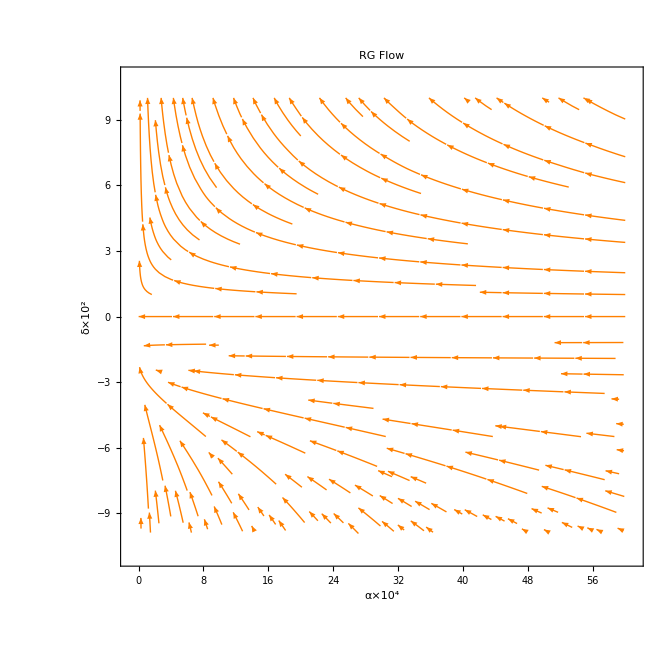

```mathematica
StreamPlot[{-1/10000^2 α^2(38/(15 π^2)+1/100(5699δ)/(1890 π^2)),(1/100(4α δ)/(945 π^2)+1/100^2(533α δ^2)/(1890 π^2))/10000},{α,0,60},{δ,-10,10},PlotLabel->"RG Flow",FrameLabel->{"α×10^4","δ×10^2"},StreamStyle->{Arrowheads[{{0.03, Automatic}}],Orange},StreamPoints->Fine]
```